```mathematica
minxplot =-5;
maxxplot = 5;
minyplot = -5;
maxyplot = 5;

μ = 1;

sol[u_, v_]:=NDSolve[{x'[t]== μ*x[t] - 5y[t] - x[t]^3,y'[t]==5x[t] + μ*y[t] + 3y[t]^3,x[0]==u,y[0]==v},{x,y},{t,10}, Method->"StiffnessSwitching"]

miny = -0.01;
maxy = 0.01;
minx = -0.01;
maxx = 0.01;
step = 0.005;

Table11= Table[{minx, y}, {y, miny, maxy, step}];
Table21 = Table[{x,maxy}, {x, minx, maxx, step}];
Table31= Table[{maxx, y}, {y, miny, maxy,step}];
Table41 = Table[{x, miny}, {x, minx, maxx, step}];

miny = -4;
maxy = 4;
minx = -4;
maxx = 4;
step = 0.2;

Table12= Table[{minx, y}, {y, miny, maxy, step}];
Table22 = Table[{x,maxy}, {x, minx, maxx, step}];
Table32= Table[{maxx, y}, {y, miny, maxy,step}];
Table42= Table[{x, miny}, {x, minx, maxx, step}];

TableFinal = Join[Table11, Table21, Table31, Table41, Table12, Table32];

Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[TableFinal[[i,1]],TableFinal[[i,2]]]], {t,0,5},PlotRange->{{minxplot,maxxplot},{minyplot,maxyplot}},PlotLabel->Style["System 1. μ = 1. Arrows denote starting points and direction. Unstable origin.",FontSize->15]]/.Line[x_]:>{Arrowheads[{0.01,0.}],Arrow[x]}, {i,Length[TableFinal]}]]
```

NDSolve::ndsz: At t == 4.134, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.62285, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.71721, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

-Graphics-

NDSolve::ndsz: At t == 0.0378824, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.0452582, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.0546481, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

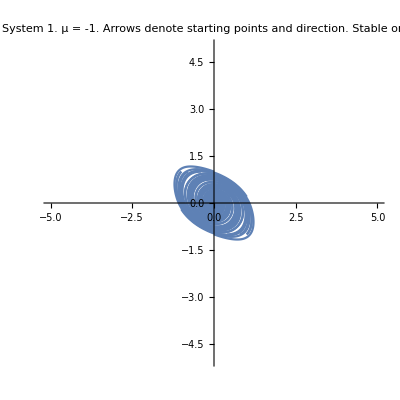

```mathematica
minxplot =-5;
maxxplot = 5;
minyplot = -5;
maxyplot = 5;

μ = -1;

sol[u_, v_]:=NDSolve[{x'[t]== μ*x[t] - 5y[t] - x[t]^3,y'[t]==5x[t] + μ*y[t] + 3y[t]^3,x[0]==u,y[0]==v},{x,y},{t,10}, Method->"StiffnessSwitching"]

miny = -2;
maxy = 2;
minx = -2;
maxx = 2;
step = 0.2;

Table11= Table[{minx, y}, {y, miny, maxy, step}];
Table21 = Table[{x,maxy}, {x, minx, maxx, step}];
Table31= Table[{maxx, y}, {y, miny, maxy,step}];
Table41 = Table[{x, miny}, {x, minx, maxx, step}];

miny = -4;
maxy = 4;
minx = -4;
maxx = 4;
step = 0.2;

Table12= Table[{minx, y}, {y, miny, maxy, step}];
Table22 = Table[{x,maxy}, {x, minx, maxx, step}];
Table32= Table[{maxx, y}, {y, miny, maxy,step}];
Table42= Table[{x, miny}, {x, minx, maxx, step}];

miny = -1;
maxy = 1;
minx = -1;
maxx = 1;
step = 0.2;

Table13= Table[{minx, y}, {y, miny, maxy, step}];
Table23 = Table[{x,maxy}, {x, minx, maxx, step}];
Table33= Table[{maxx, y}, {y, miny, maxy,step}];
Table43= Table[{x, miny}, {x, minx, maxx, step}];



TableFinal = Join[Table11, Table21, Table31, Table41, Table12, Table22, Table32,Table42, Table13, Table23, Table33, Table43];

Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[TableFinal[[i,1]],TableFinal[[i,2]]]], {t,0,5},PlotRange->{{minxplot,maxxplot},{minyplot,maxyplot}},PlotLabel->Style["System 1. μ = -1. Arrows denote starting points and direction. Stable origin.",FontSize->15]]/.Line[x_]:>{Arrowheads[{0.01,0.}],Arrow[x]}, {i,Length[TableFinal]}]]
```

```mathematica
minxplot =-1.1;
maxxplot = 1.1;
minyplot = -1.1;
maxyplot = 1.1;

μ = 0.2;

sol[u_, v_]:=NDSolve[{x'[t]== μ*x[t] + y[t] - x[t]^2,y'[t]==-x[t] + μ*y[t] + 2*x[t]^2,x[0]==u,y[0]==v},{x,y},{t,100}, Method->"StiffnessSwitching"]

miny = -0.01;
maxy = 0.01;
minx = -0.01;
maxx = 0.01;
step = 0.005;

Table11= Table[{minx, y}, {y, miny, maxy, step}];
Table21 = Table[{x,maxy}, {x, minx, maxx, step}];
Table31= Table[{maxx, y}, {y, miny, maxy,step}];
Table41 = Table[{x, miny}, {x, minx, maxx, step}];


miny = -1;
maxy = 1;
minx = -1;
maxx = 1;
step = 0.1;

Table13= Table[{minx, y}, {y, miny, maxy, step}];
Table23 = Table[{x,maxy}, {x, minx, maxx, step}];
Table33= Table[{maxx, y}, {y, miny, maxy,step}];
Table43= Table[{x, miny}, {x, minx, maxx, step}];

TableFinal = Join[Table11, Table21, Table31, Table41, Table13, Table23, Table33, Table43];

Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[TableFinal[[i,1]],TableFinal[[i,2]]]], {t,0,100},PlotRange->{{minxplot,maxxplot},{minyplot,maxyplot}},PlotLabel->Style["System 2. μ = 0.2. Arrows denote starting points and direction. Origin unstable.",FontSize->15]]/.Line[x_]:>{Arrowheads[{0.01,0.}],Arrow[x]}, {i,Length[TableFinal]}]]
```

-Graphics-

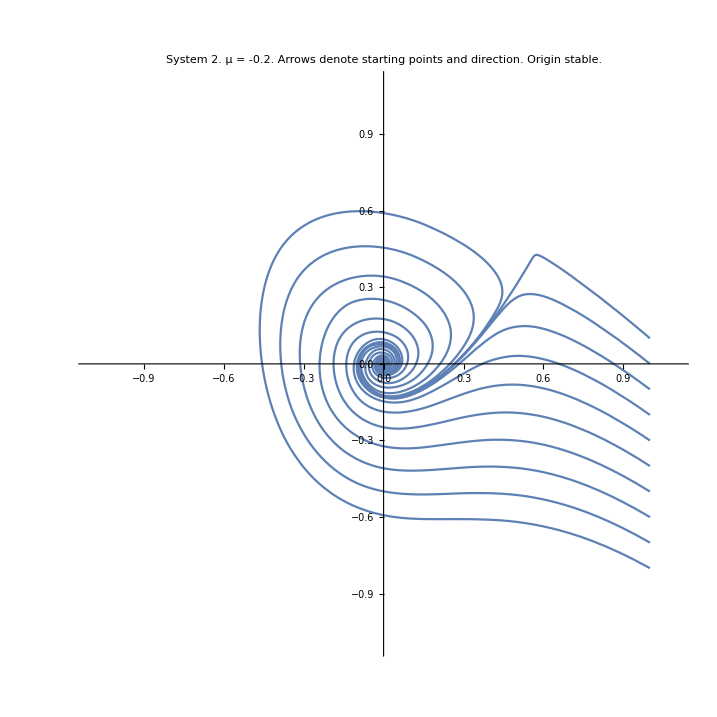

```mathematica
minxplot =-1.1;
maxxplot = 1.1;
minyplot = -1.1;
maxyplot = 1.1;

μ = -0.2;

sol[u_, v_]:=NDSolve[{x'[t]== μ*x[t] + y[t] - x[t]^2,y'[t]==-x[t] + μ*y[t] + 2*x[t]^2,x[0]==u,y[0]==v},{x,y},{t,100}, Method->"StiffnessSwitching"]



miny = -1;
maxy = 1;
minx = -1;
maxx = 1;
step = 0.1;

Table13= Table[{minx, y}, {y, miny, maxy, step}];
Table23 = Table[{x,maxy}, {x, minx, maxx, step}];
Table33= Table[{maxx, y}, {y, miny, maxy,step}];
Table43= Table[{x, miny}, {x, minx, maxx, step}];



TableFinal = Join[Table13, Table23, Table33, Table43];


Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[TableFinal[[i,1]],TableFinal[[i,2]]]], {t,0,100},PlotRange->{{minxplot,maxxplot},{minyplot,maxyplot}},PlotLabel->Style["System 2. μ = -0.2. Arrows denote starting points and direction. Origin stable.",FontSize->15]]/.Line[x_]:>{Arrowheads[{0.01,0.}],Arrow[x]}, {i,Length[TableFinal]}]]
```